## Milanesi et al . (2014)' s model

## Sliding Mode

```mathematica
equiSlide=1/2 ρ CD (Sin[π/2-θ])^3 U^2 Aref/Cos[θ] + m g Sin[θ] == μ (m g Cos[θ] -ρ g Vs Cos[θ]-1/2 ρ CD   (Sin[π/2-θ])^2 Cos[π/2-θ]/Cos[θ]  U^2 Aref )//Simplify
```

Aref CD U^2 ρ Cos[θ]^2+2 g m Sin[θ]+μ Cos[θ] (-2 g m+2 g Vs ρ+Aref CD U^2 ρ Sin[θ])==0

```mathematica
(*equiSlideSub=equiSlide/.{CD->((cda (h/Y)^2+cdb (h/Y)+cdc)(cdd((√(g Cos[θ] h))/U))*corrCD),As->(If[h/Cos[θ]≤Y/2,2(h/Cos[θ])d,((2  Y  d)/2+dd (h/Cos[θ]- (Y/2)))]),Vs->(If[h/Cos[θ]≤Y/2,2(h/Cos[θ])π (d^2/4),((2  Y π  (d^2/4))/2+(π (dd^2/4)) (h/Cos[θ]- (Y/2)))]), Aref->(5/2 d  Y Cos[θ])}//Simplify*)
```

1/Y(-4 g m Y μ Cos[θ]+5 cdd corrCD d U (cda h^2+cdb h Y+cdc Y^2) ρ Cos[θ]^4 √(g h Cos[θ])+4 g Y μ ρ Cos[θ] If[2 h Sec[θ]≤Y,(2 h π d^2)/(Cos[θ] 4),(2 Y π d^2)/(4 2)+1/4 (π dd^2) (h/Cos[θ]-Y/2)]+4 g m Y Sin[θ]+5 cdd corrCD d U (cda h^2+cdb h Y+cdc Y^2) μ ρ Cos[θ]^3 √(g h Cos[θ]) Sin[θ])==0

```mathematica
equiSlideSub=equiSlide/.{CD->(cda (h/Y)^2+cdb (h/Y)^1+cdc)*corrCD,As->(If[h/Cos[θ]≤Y/2,2(h/Cos[θ])d,((2  Y  d)/2+dd (h/Cos[θ]- (Y/2)))]),Vs->(If[h/Cos[θ]≤Y/2,2(h/Cos[θ])π (d^2/4),((2  Y π  (d^2/4))/2+(π (dd^2/4)) (h/Cos[θ]- (Y/2)))]), Aref->(5/2 d  Y )}//Simplify
```

1/Y(5 corrCD d U^2 (cda h^2+Y (cdb h+cdc Y)) ρ Cos[θ]^2+4 g Y μ ρ Cos[θ] If[2 h Sec[θ]≤Y,(2 h π d^2)/(Cos[θ] 4),(2 Y π d^2)/(4 2)+1/4 (π dd^2) (h/Cos[θ]-Y/2)]+4 g m Y Sin[θ]+μ Cos[θ] (-4 g m Y+5 corrCD d U^2 (cda h^2+cdb h Y+cdc Y^2) ρ Sin[θ]))==0

```mathematica
FindRoot[equiSlideSub/.{cda->(-4.12891), cdb->1.46206,cdc->0.24386,cdd->0.59261,corrCD->1.02,θ->(0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, U->1.0, g->9.81, μ->0.525, ρ->1000.0},{h,0.25}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{h→0.529677}

```mathematica
h/.NSolve[equiSlideSub/.{cda->(-4.12891), cdb->1.46206,cdc->0.24386,cdd->0.59261,corrCD->1.02,θ->(0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, h->0.3, g->9.81, μ->0.525, ρ->1000.0},h, PositiveReals][[1]]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

h/.{}⟦1⟧

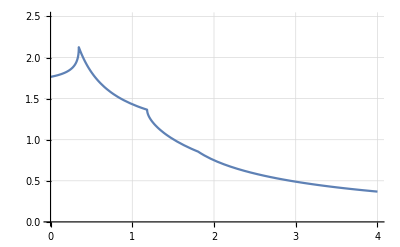

```mathematica
(*Plot[h/.FindRoot[equiSlideSub/.{cda->(-1.30781), cdb->1.10608,cdc->0.1508,cdd->0.44517,corrCD->1.02,θ->(0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.525, ρ->1000.0},{h,0.25}][[1]], {U,0,4}, PlotRange->{0,2.5} ,GridLines->Automatic]*)
```

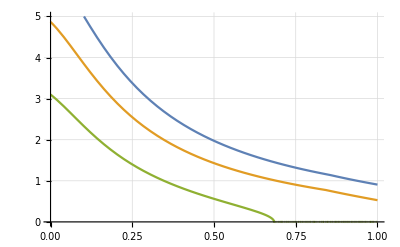

```mathematica
Plot[{U/.FindRoot[equiSlideSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0},{U,0.5}][[1]], U/.FindRoot[equiSlideSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(10.0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0},{U,0.5}][[1]], U/.FindRoot[equiSlideSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(20.0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0},{U,0.5}][[1]]}, {h,0,1}, PlotRange->{0,5.} ,GridLines->Automatic]
```

```mathematica
(*Output numerical values*)
xcoord=Table[i,{i,0.0,1.2,(1.2-0.0)/250.0}];
ucsol=Table[U/.FindRoot[equiSlideSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(20 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0, h->xcoord[[i]]},{U,0.5}][[1]],{i,1,Length[xcoord]}];
Export["G:\\underground_flooding\\dualSPHysics\\human_stability\\slope_effect\\analytical_sol\\milanesi\\sliding\\usol_20deg.txt",ucsol,"Table"]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

G:\underground_flooding\dualSPHysics\human_stability\slope_effect\analytical_sol\milanesi\sliding\usol_20deg.txt

## Toppling Mode

```mathematica
equiTop=1/2 ρ CD (Sin[π/2-θ])^3 U^2 Aref (h/2)+m g  Sin[θ](yg  Cos[θ])+ρ g Vs Cos[θ](xgs/Cos[θ]+ygs Sin[θ])+1/2 ρ CD   (Sin[π/2-θ])^2 Cos[π/2-θ] U^2 Aref (xgs/Cos[θ]+h/2 Tan[θ])==m g Cos[θ](xg/Cos[θ]+yg Sin[θ])//Simplify
```

4 g (m xg-Vs xgs ρ)==ρ Cos[θ] (Aref CD h U^2+2 (Aref CD U^2 xgs+2 g Vs ygs) Sin[θ])

```mathematica
equiTopSub=equiTop/.{CD->(cda (h/Y)^2+cdb (h/Y)^1+cdc)*corrCD,As->(If[h/Cos[θ]≤Y/2,2(h/Cos[θ])d,((2  Y  d)/2+dd (h/Cos[θ]- (Y/2)))]),Vs->(If[h/Cos[θ]≤Y/2,2(h/Cos[θ])π (d^2/4),((2  Y π  (d^2/4))/2+(π (dd^2/4)) (h/Cos[θ]- (Y/2)))]), Aref->(5/2 d  Y ), xg->(5d)/8,yg->(7Y)/12,xgs->If[h/Cos[θ]≤Y/2,d/2,(2 ((π d^2)/4)(Y/2)(d/2)+((π dd^2)/4) (h/Cos[θ]-(Y/2))(dd/2))/(2 ((π d^2)/4)(Y/2)+((π dd^2)/4) (h/Cos[θ]-(Y/2)))],ygs->If[h/Cos[θ]≤Y/2,h/(2 Cos[θ]),(2 ((π d^2)/4)(Y^2/8)+((π dd^2)/4) (h/Cos[θ]-(Y/2))(1/2(h/Cos[θ]-Y/2)+Y/2))/(2 ((π d^2)/4)(Y/2)+((π dd^2)/4) (h/Cos[θ]-(Y/2)))]}//Simplify
```

1/Y(-5 d g m Y+5 corrCD d h U^2 (cda h^2+Y (cdb h+cdc Y)) ρ Cos[θ]+4 g Y ρ If[2 h Sec[θ]≤Y,(2 h π d^2)/(Cos[θ] 4),(2 Y π d^2)/(4 2)+1/4 (π dd^2) (h/Cos[θ]-Y/2)] If[2 h Sec[θ]≤Y,h/(2 Cos[θ]),((2 (π d^2) Y^2)/(4 8)+1/4 (π dd^2) (h/Cos[θ]-Y/2) (1/2 (h/Cos[θ]-Y/2)+Y/2))/((2 (π d^2) Y)/(4 2)+1/4 (π dd^2) (h/Cos[θ]-Y/2))] Sin[2 θ]+ρ If[2 h Sec[θ]≤Y,d/2,((2 (π d^2) Y d)/(4 2 2)+((π dd^2) (h/Cos[θ]-Y/2) dd)/(4 2))/((2 (π d^2) Y)/(4 2)+1/4 (π dd^2) (h/Cos[θ]-Y/2))] (8 g Y If[2 h Sec[θ]≤Y,(2 h π d^2)/(Cos[θ] 4),(2 Y π d^2)/(4 2)+1/4 (π dd^2) (h/Cos[θ]-Y/2)]+5 corrCD d U^2 (cda h^2+cdb h Y+cdc Y^2) Sin[2 θ]))==0

```mathematica
FindRoot[equiTopSub/.{cda->(-4.12891), cdb->1.46206,cdc->0.24386,cdd->0.59261,corrCD->1.02,θ->(0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, h->0.3, g->9.81, μ->0.525, ρ->1000.0},{U,0.25}]
```

{U→1.80166}

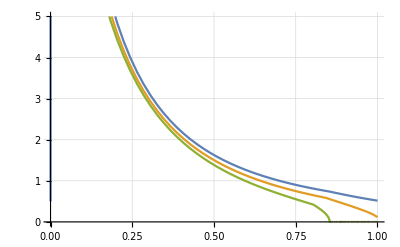

```mathematica
Plot[{U/.FindRoot[equiTopSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0},{U,0.5}][[1]], U/.FindRoot[equiTopSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(10.0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0},{U,0.5}][[1]], U/.FindRoot[equiTopSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(20.0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0},{U,0.5}][[1]]}, {h,0,1}, PlotRange->{0,5.} ,GridLines->Automatic]
```

```mathematica
(*Output numerical values*)
xcoord=Table[i,{i,0.0,1.2,(1.2-0.0)/250.0}];
ucsol=Table[U/.FindRoot[equiTopSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(20 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0, h->xcoord[[i]]},{U,0.5}][[1]],{i,1,Length[xcoord]}];
Export["G:\\underground_flooding\\dualSPHysics\\human_stability\\slope_effect\\analytical_sol\\milanesi\\toppling\\usol_20deg.txt",ucsol,"Table"]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

G:\underground_flooding\dualSPHysics\human_stability\slope_effect\analytical_sol\milanesi\toppling\usol_20deg.txt

## Milan original

```mathematica
equiSlide=1/2 ρ CD (Sin[π/2-θ])^3 U^2 As+ m g Sin[θ] == μ (m g Cos[θ] -ρ g Vs Cos[θ]-1/2 ρ CD   (Sin[π/2-θ])^2 Cos[π/2-θ] U^2 As )//Simplify
```

2 As CD U^2 ρ Cos[θ]^3+4 g m Sin[θ]+μ Cos[θ] (-4 g m+4 g Vs ρ+As CD U^2 ρ Sin[2 θ])==0

```mathematica
equiSlideSub=equiSlide/.{CD->(1)*corrCD,As->(If[h/Cos[θ]≤Y/2,2(h/Cos[θ])d,((2  Y  d)/2+dd (h/Cos[θ]- (Y/2)))]),Vs->(If[h/Cos[θ]≤Y/2,2(h/Cos[θ])π (d^2/4),((2  Y π  (d^2/4))/2+(π (dd^2/4)) (h/Cos[θ]- (Y/2)))]), Aref->(5/2 d  Y )}//Simplify
```

2 g μ ρ Cos[θ] If[2 h Sec[θ]≤Y,(2 h π d^2)/(Cos[θ] 4),(2 Y π d^2)/(4 2)+1/4 (π dd^2) (h/Cos[θ]-Y/2)]+2 g m (-μ Cos[θ]+Sin[θ])+corrCD U^2 ρ Cos[θ]^2 If[2 h Sec[θ]≤Y,(2 h d)/Cos[θ],(2 Y d)/2+dd (h/Cos[θ]-Y/2)] (Cos[θ]+μ Sin[θ])==0

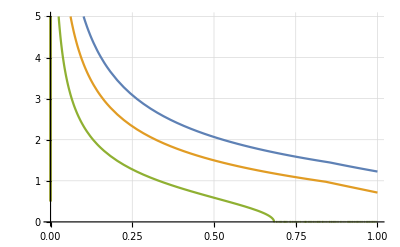

```mathematica
Plot[{U/.FindRoot[equiSlideSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0},{U,0.5}][[1]], U/.FindRoot[equiSlideSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(10.0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0},{U,0.5}][[1]], U/.FindRoot[equiSlideSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(20.0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0},{U,0.5}][[1]]}, {h,0,1}, PlotRange->{0,5.} ,GridLines->Automatic]
```

```mathematica
(*Output numerical values*)
xcoord=Table[i,{i,0.0,1.2,(1.2-0.0)/250.0}];
ucsol=Table[U/.FindRoot[equiSlideSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(20 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0, h->xcoord[[i]]},{U,0.5}][[1]],{i,1,Length[xcoord]}];
Export["G:\\underground_flooding\\dualSPHysics\\human_stability\\slope_effect\\analytical_sol\\milanesi\\sliding\\usol_orig_20deg.txt",ucsol,"Table"]
```

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {U} = {0.5}.

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

G:\underground_flooding\dualSPHysics\human_stability\slope_effect\analytical_sol\milanesi\sliding\usol_orig_20deg.txt

```mathematica
equiTop=1/2 ρ CD (Sin[π/2-θ])^3 U^2 As (h/2)+m g  Sin[θ](yg  Cos[θ])+ρ g Vs Cos[θ](xgs/Cos[θ]+ygs Sin[θ])+1/2 ρ CD   (Sin[π/2-θ])^2 Cos[π/2-θ] U^2 As (xgs/Cos[θ]+h/2 Tan[θ])==m g Cos[θ](xg/Cos[θ]+yg Sin[θ])//Simplify
```

4 g (m xg-Vs xgs ρ)==ρ Cos[θ] (As CD h U^2+2 (As CD U^2 xgs+2 g Vs ygs) Sin[θ])

```mathematica
equiTopSub=equiTop/.{CD->1*corrCD,As->(If[h/Cos[θ]≤Y/2,2(h/Cos[θ])d,((2  Y  d)/2+dd (h/Cos[θ]- (Y/2)))]),Vs->(If[h/Cos[θ]≤Y/2,2(h/Cos[θ])π (d^2/4),((2  Y π  (d^2/4))/2+(π (dd^2/4)) (h/Cos[θ]- (Y/2)))]), Aref->(5/2 d  Y ), xg->(5d)/8,yg->(7Y)/12,xgs->If[h/Cos[θ]≤Y/2,d/2,(2 ((π d^2)/4)(Y/2)(d/2)+((π dd^2)/4) (h/Cos[θ]-(Y/2))(dd/2))/(2 ((π d^2)/4)(Y/2)+((π dd^2)/4) (h/Cos[θ]-(Y/2)))],ygs->If[h/Cos[θ]≤Y/2,h/(2 Cos[θ]),(2 ((π d^2)/4)(Y^2/8)+((π dd^2)/4) (h/Cos[θ]-(Y/2))(1/2(h/Cos[θ]-Y/2)+Y/2))/(2 ((π d^2)/4)(Y/2)+((π dd^2)/4) (h/Cos[θ]-(Y/2)))]}//Simplify
```

(5 d g m)/2==ρ Cos[θ] (corrCD h U^2 If[2 h Sec[θ]≤Y,(2 h d)/Cos[θ],(2 Y d)/2+dd (h/Cos[θ]-Y/2)]+4 g If[2 h Sec[θ]≤Y,(2 h π d^2)/(Cos[θ] 4),(2 Y π d^2)/(4 2)+1/4 (π dd^2) (h/Cos[θ]-Y/2)] If[2 h Sec[θ]≤Y,h/(2 Cos[θ]),((2 (π d^2) Y^2)/(4 8)+1/4 (π dd^2) (h/Cos[θ]-Y/2) (1/2 (h/Cos[θ]-Y/2)+Y/2))/((2 (π d^2) Y)/(4 2)+1/4 (π dd^2) (h/Cos[θ]-Y/2))] Sin[θ])+ρ If[2 h Sec[θ]≤Y,d/2,((2 (π d^2) Y d)/(4 2 2)+((π dd^2) (h/Cos[θ]-Y/2) dd)/(4 2))/((2 (π d^2) Y)/(4 2)+1/4 (π dd^2) (h/Cos[θ]-Y/2))] (4 g If[2 h Sec[θ]≤Y,(2 h π d^2)/(Cos[θ] 4),(2 Y π d^2)/(4 2)+1/4 (π dd^2) (h/Cos[θ]-Y/2)]+corrCD U^2 If[2 h Sec[θ]≤Y,(2 h d)/Cos[θ],(2 Y d)/2+dd (h/Cos[θ]-Y/2)] Sin[2 θ])

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

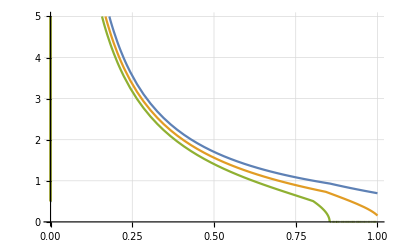

```mathematica
Plot[{U/.FindRoot[equiTopSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0},{U,0.5}][[1]], U/.FindRoot[equiTopSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(10.0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0},{U,0.5}][[1]], U/.FindRoot[equiTopSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(20.0 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0},{U,0.5}][[1]]}, {h,0,1}, PlotRange->{0,5.} ,GridLines->Automatic]
```

```mathematica
(*Output numerical values*)
xcoord=Table[i,{i,0.0,1.2,(1.2-0.0)/250.0}];
ucsol=Table[U/.FindRoot[equiTopSub/.{cda->2.16748, cdb->0.13654,cdc->0.03133 ,corrCD->1.02,θ->(20 Degree),Y->1.71,m->71.0,dd->0.26,d->0.13, g->9.81, μ->0.50, ρ->1000.0, h->xcoord[[i]]},{U,0.5}][[1]],{i,1,Length[xcoord]}];
Export["G:\\underground_flooding\\dualSPHysics\\human_stability\\slope_effect\\analytical_sol\\milanesi\\toppling\\usol_orig_20deg.txt",ucsol,"Table"]
```

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {U} = {0.5}.

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

G:\underground_flooding\dualSPHysics\human_stability\slope_effect\analytical_sol\milanesi\toppling\usol_orig_20deg.txt